-Graphics-

Obvod je napájen střídavým zdrojem napětí uZ (t) = amplituda*sin (2*π*f*t), kde amplituda je 10 V a frekvence f = 1000 Hz . Hodnoty součástek jsou 
R1 = 100 Ω, R2 = 100 Ω, R3 = 500 Ω, C1 = 50 nF, C2 = 1 μF, L1 = 56 mH a L2 = 13 mH. Vyřešte:
     	1. Pomocí metody uzlových napětí vytvořte soustavu rovnic pro časovou oblast a vypočítejte všechna uzlová napětí, která zobrazíte do 1 grafu . (DU3a - 1 bod)
     		Poznámka: Při řešení v NDSolve použijte tyto optimalizační parametry:  StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}
	2. Uvedený zdroj převeďte na fázor uZf a řešte obvod v HUSu . (DU3b - 1 bod)
	3. Za předpokladu že uZ = 10 V převeďte obvod do stejnosměrného stavu a vypočtěte napětí uout . 	(DU3c - 1 bod)

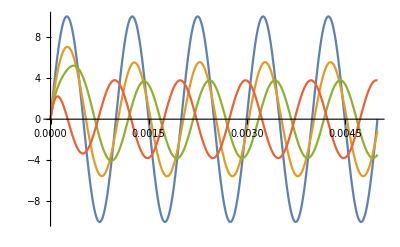

```mathematica
ClearAll["Global`*"]


amplituda = 10;
frekvence = 1000;
perioda = 1/frekvence;
tmax = 5*perioda;
in = {uZ[t]-> amplituda*Sin[2*π*frekvence * t]};

uzel1 = 0 == iUz[t]+iR1[t]+iC1[t];
uzel2= iR1[t]+iC1[t]==iR2[t]+iL1[t];
uzel3=iR2[t]+iL1[t]==iC2[t];
uzel4= iC2[t]==iR3[t]+iL2[t];

rezistor1 = iR1[t]*R1==u1[t]-u2[t];
rezistor2 = iR2[t]*R2==u2[t]-u3[t];
rezistor3 = iR3[t]*R3==u4[t];
civka1 = iL1'[t]*L1 == u2[t]-u3[t];
civka2 = iL2'[t]*L2 == u4[t] ;
kond1 = iC1[t]==C1*(u1'[t]-u2'[t]);
kond2=iC2[t]==C2*(u3'[t]-u4'[t]);

pp1=iL1[0]==0;
pp2=iL2[0]==0;
pp3=u1[0]==0;
pp4=u2[0]==0;
pp5=u3[0]==0;
pp6=u4[0]==0;

zdroj = uZ[t]==u1[t];

rovnice = {uzel1, uzel2, uzel3, uzel4, rezistor1, rezistor2, rezistor3, civka1, civka2, kond1, kond2, pp1, pp2, pp3, pp4,pp5, pp6, zdroj};

nezname = {u1[t], u2[t], u3[t], u4[t],iUz[t], iR1[t], iR2[t], iR3[t], iL1[t], iL2[t], iC1[t], iC2[t]};

soucastky = {R1 -> 100, R2->100, R3-> 500, C1-> 50*10^-9, C2->1*10^-6, L1->56*10^-3, L2->13*10^-3};

reseni = NDSolve[rovnice /. soucastky /. in, nezname,{t,0,tmax}, StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}];

Plot[{u1[t]/. reseni, u2[t]/.reseni, u3[t]/.reseni, u4[t]/.reseni}, {t, 0, tmax}]
```

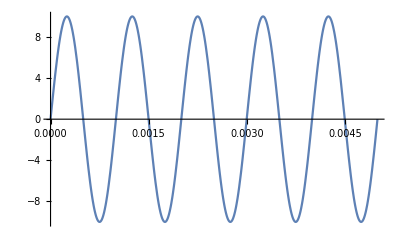

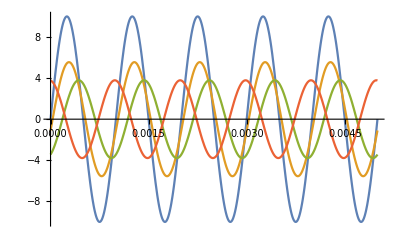

```mathematica
(* RESENI V HUSU *)
ClearAll["Global`*"]

soucastky = {R1 -> 100, R2->100, R3-> 500, C1-> 50*10^-9, C2->1*10^-6, L1->56*10^-3, L2->13*10^-3};

amplituda = 10;
frekvence = 1000;
perioda = 1/frekvence;
tmax = 5*perioda;
omega = {ω->2*π*frekvence};
in= amplituda*Sin[ω * t]/.omega;
uZf = amplituda*ⅇ^(ⅉ*0);
Plot[Im[uZf * ⅇ^(ⅉ*ω*t)/.omega], {t, 0, tmax}]

uzel1 = 0 == iUz+iR1+iC1;
uzel2= iR1+iC1==iR2+iL1;
uzel3=iR2+iL1==iC2;
uzel4= iC2 ==iR3+iL2;

rezistor1 = iR1*R1==u1-u2;
rezistor2 = iR2*R2==u2-u3;
rezistor3 = iR3*R3==u4;
civka1 = ⅉ*ω*iL1*L1 == u2-u3;
civka2 = ⅉ*ω*iL2*L2 == u4 ;
kond1 = 1/(ⅉ*ω*C1)*iC1==u1-u2;
kond2=1/(ⅉ*ω*C2)*iC2==u3-u4;

zdroj = uZf==u1;
out = uOut==u4;

rovnice = {uzel1, uzel2, uzel3, uzel4, rezistor1, rezistor2, rezistor3, civka1, civka2, kond1, kond2, zdroj, out};

nezname = {u1, u2, u3, u4,iUz, iR1, iR2, iR3, iL1, iL2, iC1, iC2, uOut};

reseni = Solve[rovnice /. soucastky , nezname];

Plot[{Im[(u1/.reseni)*ⅇ^(ⅉ*ω*t)/.omega], Im[(u2/.reseni)*ⅇ^(ⅉ*ω*t)/.omega], Im[(u3/.reseni)*ⅇ^(ⅉ*ω*t)/.omega], Im[(u4/.reseni)*ⅇ^(ⅉ*ω*t)/.omega]},{t,0,tmax}]
```

```mathematica
(*vysledek po prevedeni do stejnosmerneho proudu uout je 0*)
```